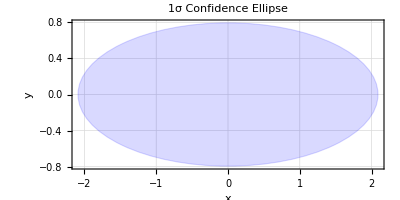

```mathematica
CovEllipse[Σ_]:=Module[{λ,v,angle},{λ,v}=Eigensystem[Σ];
angle=ArcTan[v[[1,1]],v[[1,2]]];
Graphics[{Blue,Opacity[0.15],EdgeForm[{Blue,Thick}],Rotate[Ellipsoid[{0,0},Sqrt[λ]],angle,{0,0}]},Axes->True,Frame->True,FrameLabel->{"x","y"},PlotLabel->"1σ Confidence Ellipse",GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->400]]

(*Usage*)
CovEllipse[{{3,1.8},{1.8,2}}]
```

```mathematica
params={lM->3,lm->1};
```

```mathematica
Σ0=({{lM, 0}, {0, lm}});
R[φ_]=RotationMatrix[φ]
```

{{Cos[φ],-Sin[φ]},{Sin[φ],Cos[φ]}}

```mathematica
Manipulate[CovEllipse[R[φ].Σ0.R[-φ]/.params],{φ,0,2π}]
```

```mathematica
ρ[φ]R[φ].Σ0.R[φ]ᵀ//Simplify//MatrixForm
```

((lM Cos[φ]^2+lm Sin[φ]^2) ρ[φ] | -((lm-lM) Cos[φ] Sin[φ] ρ[φ])
-((lm-lM) Cos[φ] Sin[φ] ρ[φ]) | (lm Cos[φ]^2+lM Sin[φ]^2) ρ[φ])

```mathematica
R[φ].({{1, 0}, {0, -1}}).R[-φ]//Simplify
```

{{Cos[2 φ],Sin[2 φ]},{Sin[2 φ],-Cos[2 φ]}}